```mathematica
(* Import data for Broadmann connectome *)
```

```mathematica
connBroadmann=Import["/Users/gaia0/Documenti/Didattica/Tesi/Broadmann82.edge"];
```

```mathematica
vertBroadmann=Import["/Users/gaia0/Documenti/Didattica/Tesi/Broadmann82.node"];
```

```mathematica
(* Select Talairach (x,y)-coordinates and labels *)
```

```mathematica
vertcoord=vertBroadmann[[1;;,{1,2}]];
vertlabel=vertBroadmann[[1;;,{6}]];
```

```mathematica
MatrixForm[vertlabel] MatrixForm[vertcoord]
```

(1L
1R
2L
2R
3L
3R
4L
4R
5L
5R
6L
6R
7L
7R
8L
8R
9L
9R
10L
10R
11L
11R
17L
17R
18L
18R
19L
19R
20L
20R
21L
21R
22L
22R
23L
23R
24L
24R
25L
25R
26L
26R
27L
27R
28L
28R
29L
29R
30L
30R
32L
32R
34L
34R
35L
35R
36L
36R
37L
37R
38L
38R
39L
39R
40L
40R
41L
41R
42L
42R
43L
43R
44L
44R
45L
45R
46L
46R
47L
47R
48L
48R) (-43.347 | -33.267
36.017 | -34.877
-46.592 | -34.283
43.042 | -34.882
-41.124 | -26.628
38.726 | -26.779
-27.911 | -22.877
26.884 | -22.774
-11.711 | -50.335
10.565 | -50.376
-28.722 | -3.387
26.821 | -3.144
-21.962 | -64.89
20.152 | -64.938
-18.278 | 22.911
16.811 | 23.184
-24.594 | 37.32
22.509 | 37.266
-16.038 | 59.012
13.505 | 59.285
-15.868 | 41.999
14.287 | 41.912
-11.367 | -77.659
9.722 | -80.832
-17.944 | -79.578
15.445 | -80.241
-31.112 | -73.468
28.645 | -73.589
-46.697 | -17.316
44.482 | -18.356
-58.701 | -22.674
56.124 | -24.4
-62.09 | -27.757
59.074 | -28.558
-7.35 | -37.121
6.353 | -38.471
-5.127 | 17.481
3.935 | 17.297
-7.702 | 16.525
6.237 | 15.268
-7.569 | -41.384
5.975 | -41.549
-15.386 | -36.466
13.866 | -36.568
-20.746 | 2.123
17.748 | 1.104
-9.363 | -43.442
8.147 | -43.753
-16.732 | -36.233
14.316 | -36.41
-10.995 | 33.958
9.428 | 33.952
-25.029 | -0.127
22.75 | -0.258
-16.494 | -12.319
14.662 | -12.248
-28.581 | 2.414
25.405 | 1.032
-40.675 | -51.795
39.008 | -51.835
-45.029 | 18.096
41.101 | 17.843
-45.702 | -63.239
43.234 | -63.01
-46.866 | -44.705
43.95 | -44.701
-43.761 | -39.447
41.665 | -39.463
-58.73 | -35.916
56.621 | -35.952
-63.212 | -7.812
60.264 | -8.114
-48.196 | 14.902
46.225 | 14.941
-49.053 | 33.661
46.494 | 33.754
-36.422 | 44.641
34.233 | 44.927
-35.645 | 35.003
33.515 | 34.987
-41.123 | -4.011
38.852 | -4.035)

```mathematica
(* Plot connection matrix *)
```

```mathematica
MatrixPlot[connBroadmann,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(* Plot full graph with numbered vertices in Talairach coordinates *)
```

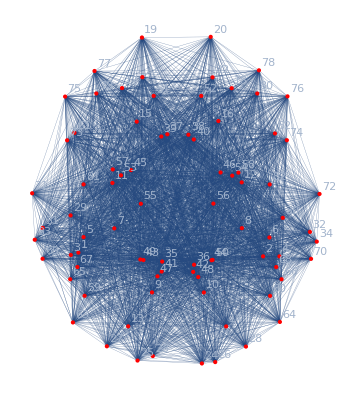

```mathematica
GraphPlot[connBroadmann,VertexCoordinates->vertcoord,VertexLabels->Automatic,PlotStyle->Thickness[0.0005],VertexShapeFunction->Function[{p},{PointSize[Large],Red,Point[p]}]]
```

```mathematica
(* Plot full graph with labelled vertices in Talairach coordinates *)
```

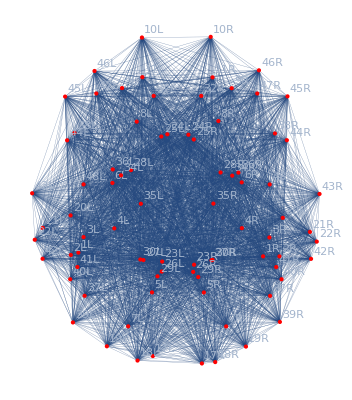

```mathematica
GraphPlot[connBroadmann,VertexCoordinates->vertcoord,VertexLabels->Table[i->vertlabel[[i]],{i,82}],PlotStyle->Thickness[0.0005],VertexShapeFunction->Function[{p},{PointSize[Large],Red,Point[p]}]]
```

```mathematica
nv=Length[connBroadmann];
```

```mathematica
(* Find adjacency matrix with connection i->j if Subscript[c, ij]>x *)
```

```mathematica
x=0.9; 
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
MatrixPlot[L1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(* Plot graph - with loops - from adjacency matrix *)
```

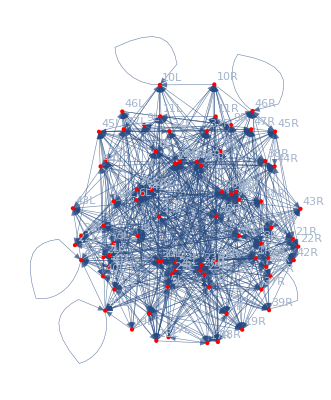

```mathematica
g1=AdjacencyGraph[L1,VertexCoordinates->vertcoord,VertexLabels->Table[i->vertlabel[[i]],{i,nv}],EdgeStyle->Thickness[0.001],VertexShapeFunction->Function[{p},{PointSize[Large],Red,Point[p]}]]
```

```mathematica
(* Plot graph - without loops - from adjacency matrix *)
```

```mathematica
L10=L1;  For[i=1,i≤nv,i++,L10[[i,i]]=0];
```

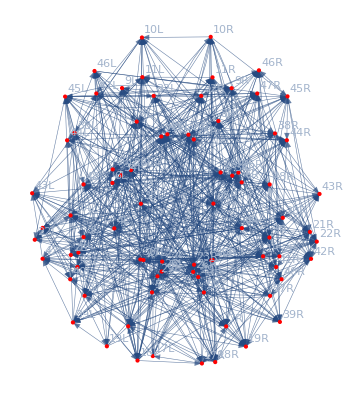

```mathematica
g10=AdjacencyGraph[L10,VertexCoordinates->vertcoord,VertexLabels->Table[i->vertlabel[[i]],{i,nv}],EdgeStyle->Thickness[0.001],VertexShapeFunction->Function[{p},{PointSize[Large],Red,Point[p]}]]
```

```mathematica
(* Set initial condition Lini[[i]]=1 if i∈iCog, Lini[[i]]=0 otherwise *)
```

```mathematica
iCog={2,4,8,9,10,15,19,21,28,35,39,41,63,64,75,79};
```

```mathematica
Lini=Table[0,nv]; Lini[[iCog]]=1;
```

```mathematica
(* Set constants a, b for the evolution rule, and maximum time *)
```

```mathematica
x=0.88; 
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
a=1; b=4; tmax=500;
PositionsMatrix=Map[Flatten,Position[#,1]&/@L1];
L2=Lini; L2out=Lini;
```

```mathematica
RuleN[m_]:=If[Sum[L2[[PositionsMatrix[[m,i]]]],{i,1,Length[PositionsMatrix[[m]]]}]>=a&& Sum[L2[[PositionsMatrix[[m,i]]]],{i,1,Length[PositionsMatrix[[m]]]}]<=b,L2out[[m]]=1,L2out[[m]]=0];
L3=Table[RuleN,nv];
TimeStepsN=Table[L2=Table[L3[[m]]@m,{m,1,nv}],{tmax}];
```

```mathematica
(* Plot state evolution for 400≤t≤500 *)
```

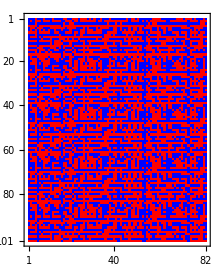

```mathematica
MatrixPlot[TimeStepsN[[400;;]],ColorRules->{0->Red,1->Blue}]
```

```mathematica
(* colors[L_]:=L/.{0->Red,1->Blue}
Manipulate[ Quiet[GraphPlot[L10,VertexCoordinates->vertcoord,EdgeStyle->Thickness[0.001],VertexStyle->Table[i->(colors/@TimeStepsN[[t]])[[i]],{i,1,nv}],VertexSize->5]],{t,1,tmax,1},SaveDefinitions->True]*)
```

```mathematica
(* Find vertices with trivial dynamics and remove them *)
```

```mathematica
trivial0=ConstantArray[0,tmax];
```

```mathematica
trivial1=ConstantArray[1,tmax];
```

```mathematica
trivInd={};For[i=1,i≤nv,i++,If[HammingDistance[Transpose[TimeStepsN][[i]],trivial0 ]≤ 10||HammingDistance[Transpose[TimeStepsN][[i]],trivial1 ]≤ 10,trivInd=Join[trivInd,{i}],trivInd=trivInd]];
```

```mathematica
trivInd
```

{}

```mathematica
ntInd=Complement[Table[i,{i,nv}],trivInd];
```

```mathematica
ntTimeStepsN=TimeStepsN[[1;;,ntInd]];
```

```mathematica
ntCorr1=Correlation[0.5 ntTimeStepsN+0.5];
```

```mathematica
MatrixPlot[ntCorr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ntnv=Length[ntInd];
```

```mathematica
z=0.87; 
Corr3=Table[Table[If[Abs[ntCorr1[[i,j]]]>z,1,0],{j,1,ntnv}],{i,1,ntnv}];
MatrixPlot[Corr3,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(* PC3=Position[Corr3,1];
```

```mathematica
(* PC4=PC3;
```

```mathematica
(* Do[If[PC3[[i]][[1]]==PC3[[i]][[2]],PC4[[i]]=DeleteDuplicates[PC3[[i]]],PC4[[i]]=PC3[[i]]],{i,Length[PC3]}];
```

```mathematica
(* PC5=DeleteDuplicates[PC4];
```

```mathematica
(* lPC5=Table[Length[PC5[[i]]],{i,Length[PC5]}];
```

```mathematica
(* iPC5=Position[lPC5,2];
```

```mathematica
(* Extract[PC5,iPC5]
```

```mathematica
ciCorr3=Table[Position[Corr3[[i]],1],{i,Length[Corr3]}];
ciCorr3
```

{{{1}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{11}},{{12}},{{13}},{{14},{63}},{{15},{36}},{{16}},{{17}},{{18},{31},{67}},{{19}},{{20}},{{21}},{{22},{69}},{{23},{31}},{{24}},{{25}},{{26}},{{27},{70}},{{28}},{{29},{75}},{{30}},{{18},{23},{31}},{{32}},{{33},{45},{76}},{{34}},{{35}},{{15},{36}},{{37}},{{38},{46},{51},{61},{69}},{{39},{67}},{{40}},{{41}},{{42}},{{43}},{{44}},{{33},{45}},{{38},{46},{61},{69}},{{47}},{{48}},{{49}},{{50},{66}},{{38},{51},{61}},{{52}},{{53}},{{54}},{{55}},{{56}},{{57}},{{58}},{{59}},{{60}},{{38},{46},{51},{61},{69}},{{62}},{{14},{63}},{{64}},{{65}},{{50},{66}},{{18},{39},{67}},{{68}},{{22},{38},{46},{61},{69}},{{27},{70}},{{71}},{{72}},{{73}},{{74}},{{29},{75}},{{33},{76}},{{77}},{{78}},{{79}},{{80}},{{81}},{{82}}}

```mathematica
leciCorr3=Table[Length[ciCorr3[[i]]],{i,Length[Corr3]}];
leciCorr3
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,3,1,1,1,2,2,1,1,1,2,1,2,1,3,1,3,1,1,2,1,5,2,1,1,1,1,1,2,4,1,1,1,2,3,1,1,1,1,1,1,1,1,1,5,1,2,1,1,2,3,1,5,2,1,1,1,1,2,2,1,1,1,1,1,1}

```mathematica
pole2ciCorr3=Position[leciCorr3,2];
pole2ciCorr3
```

{{14},{15},{22},{23},{27},{29},{36},{39},{45},{50},{63},{66},{70},{75},{76}}

```mathematica
pole3ciCorr3=Position[leciCorr3,3];
```

```mathematica
pole4ciCorr3=Position[leciCorr3,4];
```

```mathematica
cile2=Extract[ciCorr3,pole2ciCorr3];
cile2
```

{{{14},{63}},{{15},{36}},{{22},{69}},{{23},{31}},{{27},{70}},{{29},{75}},{{15},{36}},{{39},{67}},{{33},{45}},{{50},{66}},{{14},{63}},{{50},{66}},{{27},{70}},{{29},{75}},{{33},{76}}}

```mathematica
cile3=Extract[ciCorr3,pole3ciCorr3];
cile3
```

{{{18},{31},{67}},{{18},{23},{31}},{{33},{45},{76}},{{38},{51},{61}},{{18},{39},{67}}}

```mathematica
cile4=Extract[ciCorr3,pole4ciCorr3];
```

```mathematica
ci2=Table[Transpose[cile2[[i]]][[1]],{i,Length[cile2]}]
```

{{14,63},{15,36},{22,69},{23,31},{27,70},{29,75},{15,36},{39,67},{33,45},{50,66},{14,63},{50,66},{27,70},{29,75},{33,76}}

```mathematica
ci3=Table[Transpose[cile3[[i]]][[1]],{i,Length[cile3]}]
```

{{18,31,67},{18,23,31},{33,45,76},{38,51,61},{18,39,67}}

```mathematica
ci4=Table[Transpose[cile4[[i]]][[1]],{i,Length[cile4]}]
```

{{38,46,61,69}}

```mathematica
ci=DeleteDuplicates[Join[ci2,ci3,ci4]]
```

{{14,63},{15,36},{22,69},{23,31},{27,70},{29,75},{39,67},{33,45},{50,66},{33,76},{18,31,67},{18,23,31},{33,45,76},{38,51,61},{18,39,67},{38,46,61,69}}

```mathematica
tabci=Table[Table[Intersection[ci[[i]],ci[[j]]],{j,Length[ci]}],{i,Length[ci]}];
```

```mathematica
MatrixForm[tabci]
```

({14,63} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {15,36} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {22,69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {69}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {} | {31} | {23,31} | {} | {} | {} | {}
{} | {} | {} | {} | {27,70} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {29,75} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {67} | {} | {} | {} | {39,67} | {}
{} | {} | {} | {} | {} | {} | {} | {33,45} | {} | {33} | {} | {} | {33,45} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {} | {50,66} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {33} | {} | {33,76} | {} | {} | {33,76} | {} | {} | {}
{} | {} | {} | {31} | {} | {} | {67} | {} | {} | {} | {18,31,67} | {18,31} | {} | {} | {18,67} | {}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {} | {18,31} | {18,23,31} | {} | {} | {18} | {}
{} | {} | {} | {} | {} | {} | {} | {33,45} | {} | {33,76} | {} | {} | {33,45,76} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,51,61} | {} | {38,61}
{} | {} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {18,67} | {18} | {} | {} | {18,39,67} | {}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,61} | {} | {38,46,61,69})

```mathematica
tableci=Table[Table[Length[tabci[[i,j]]]/Length[tabci[[i,i]]],{i,Length[ci]}],{j,Length[ci]}];
```

```mathematica
MatrixForm[tableci]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 2/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/2 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1 | 2/3 | 0 | 0 | 2/3 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1 | 0 | 0 | 1/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2/3 | 1/3 | 0 | 0 | 1 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 1)

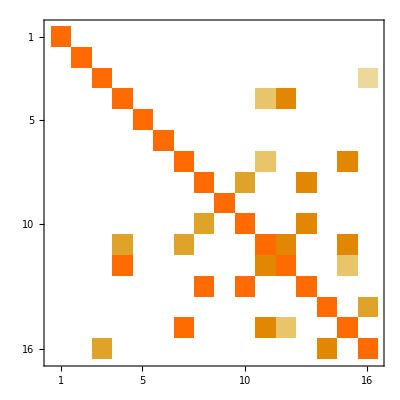

```mathematica
MatrixPlot[tableci]
```

```mathematica
(* Tests on brain circuits *)
```

```mathematica
(* x=0.88, a=1, b=4, tmax 500, z=0.87
```

```mathematica
x=0.88; a=1; b=4; tmax 500; z=0.87;
```

```mathematica
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
PositionsMatrix=Map[Flatten,Position[#,1]&/@L1];
L2=Lini; L2out=Lini;
TimeStepsN=Table[L2=Table[L3[[m]]@m,{m,1,nv}],{tmax}];
```

```mathematica
trivial0=ConstantArray[0,tmax];
trivial1=ConstantArray[1,tmax];
trivInd={};For[i=1,i≤nv,i++,If[HammingDistance[Transpose[TimeStepsN][[i]],trivial0 ]≤ 10||HammingDistance[Transpose[TimeStepsN][[i]],trivial1 ]≤ 10,trivInd=Join[trivInd,{i}],trivInd=trivInd]];
ntInd=Complement[Table[i,{i,nv}],trivInd];
ntTimeStepsN=TimeStepsN[[1;;,ntInd]];
```

```mathematica
ntCorr0=Correlation[0.5 ntTimeStepsN+0.5];
ntnv=Length[ntInd];
ntCorr1=Table[Table[If[Abs[ntCorr0[[i,j]]]>z,1,0],{j,1,ntnv}],{i,1,ntnv}];
MatrixPlot[ntCorr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ci=Table[Position[ntCorr1[[i]],1],{i,Length[ntCorr1]}];
leci=Table[Length[ci[[i]]],{i,Length[ntCorr1]}];
poleci=Table[Position[leci,i],{i,1,Max[leci]}];
cile=Table[Extract[ci,poleci[[i]]],{i,1,Max[leci]}];
circ=Flatten[Table[DeleteDuplicates[Table[Flatten[cile[[j,i]],1],{i,Length[cile[[j]]]}]],{j,2,Max[leci]}],1];
```

```mathematica
tabcirc=Table[Table[Intersection[circ[[i]],circ[[j]]],{j,Length[circ]}],{i,Length[circ]}];
```

```mathematica
MatrixForm[tabcirc]
```

({14,63} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {15,36} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {22,69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {69} | {69} | {22,69}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {} | {31} | {23,31} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {27,70} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {29,75} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {67} | {} | {} | {} | {39,67} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {33,45} | {} | {33} | {} | {} | {33,45} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {} | {50,66} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {33} | {} | {33,76} | {} | {} | {33,76} | {} | {} | {} | {} | {}
{} | {} | {} | {31} | {} | {} | {67} | {} | {} | {} | {18,31,67} | {18,31} | {} | {} | {18,67} | {} | {} | {}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {} | {18,31} | {18,23,31} | {} | {} | {18} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {33,45} | {} | {33,76} | {} | {} | {33,45,76} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,51,61} | {} | {38,61} | {38,51,61} | {38,61}
{} | {} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {18,67} | {18} | {} | {} | {18,39,67} | {} | {} | {}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,61} | {} | {38,46,61,69} | {38,46,61,69} | {38,46,61,69}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,51,61} | {} | {38,46,61,69} | {38,46,51,61,69} | {38,46,61,69}
{} | {} | {22,69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,61} | {} | {38,46,61,69} | {38,46,61,69} | {22,38,46,61,69})

```mathematica
tablecirc=Table[Table[Length[tabcirc[[i,j]]]/Length[tabcirc[[i,i]]],{i,Length[circ]}],{j,Length[circ]}];
```

```mathematica
MatrixForm[tablecirc]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1/5 | 2/5
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/2 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1 | 2/3 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1 | 0 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/2 | 3/5 | 2/5
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2/3 | 1/3 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 1 | 4/5 | 4/5
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 4/5
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 1 | 4/5 | 1)

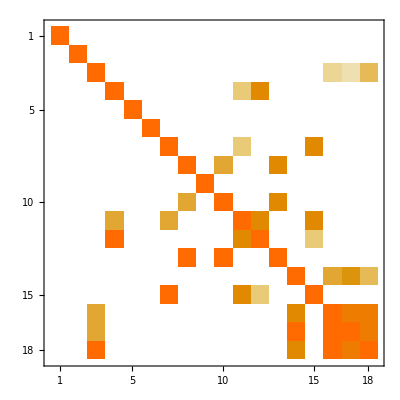

```mathematica
MatrixPlot[tablecirc]
```

```mathematica
(* x=0.88, a=1, b=4, tmax 500, z=0.88
```

```mathematica
x=0.88; a=1; b=4; tmax 500; z=0.88;
```

```mathematica
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
PositionsMatrix=Map[Flatten,Position[#,1]&/@L1];
L2=Lini; L2out=Lini;
TimeStepsN=Table[L2=Table[L3[[m]]@m,{m,1,nv}],{tmax}];
```

```mathematica
trivial0=ConstantArray[0,tmax];
trivial1=ConstantArray[1,tmax];
trivInd={};For[i=1,i≤nv,i++,If[HammingDistance[Transpose[TimeStepsN][[i]],trivial0 ]≤ 10||HammingDistance[Transpose[TimeStepsN][[i]],trivial1 ]≤ 10,trivInd=Join[trivInd,{i}],trivInd=trivInd]];
ntInd=Complement[Table[i,{i,nv}],trivInd];
ntTimeStepsN=TimeStepsN[[1;;,ntInd]];
```

```mathematica
ntCorr0=Correlation[0.5 ntTimeStepsN+0.5];
ntnv=Length[ntInd];
ntCorr1=Table[Table[If[Abs[ntCorr0[[i,j]]]>z,1,0],{j,1,ntnv}],{i,1,ntnv}];
MatrixPlot[ntCorr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ci=Table[Position[ntCorr1[[i]],1],{i,Length[ntCorr1]}];
leci=Table[Length[ci[[i]]],{i,Length[ntCorr1]}];
poleci=Table[Position[leci,i],{i,1,Max[leci]}];
cile=Table[Extract[ci,poleci[[i]]],{i,1,Max[leci]}];
circ=Flatten[Table[DeleteDuplicates[Table[Flatten[cile[[j,i]],1],{i,Length[cile[[j]]]}]],{j,2,Max[leci]}],1];
```

```mathematica
tabcirc=Table[Table[Intersection[circ[[i]],circ[[j]]],{j,Length[circ]}],{i,Length[circ]}];
```

```mathematica
MatrixForm[tabcirc]
```

({14,63} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {15,36} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {22,69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {69} | {} | {} | {69} | {69} | {22,69}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {31} | {23,31} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {27,70} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {67} | {} | {} | {} | {} | {39,67} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {33,45} | {} | {33} | {} | {} | {33,45} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {50,66} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {33} | {} | {33,76} | {} | {} | {33,76} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {31} | {} | {67} | {} | {} | {} | {18,31,67} | {18,31} | {} | {} | {} | {18,67} | {} | {} | {}
{} | {} | {} | {23,31} | {} | {} | {} | {} | {} | {18,31} | {18,23,31} | {} | {} | {} | {18} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {33,45} | {} | {33,76} | {} | {} | {33,45,76} | {} | {} | {} | {} | {} | {}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {46,61,69} | {61} | {} | {61,69} | {46,61,69} | {46,61,69}
{} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {61} | {38,51,61} | {} | {38,51,61} | {38,51,61} | {38,61}
{} | {} | {} | {} | {} | {39,67} | {} | {} | {} | {18,67} | {18} | {} | {} | {} | {18,39,67} | {} | {} | {}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {61,69} | {38,51,61} | {} | {38,51,61,69} | {38,51,61,69} | {38,61,69}
{} | {} | {69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {46,61,69} | {38,51,61} | {} | {38,51,61,69} | {38,46,51,61,69} | {38,46,61,69}
{} | {} | {22,69} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {46,61,69} | {38,61} | {} | {38,61,69} | {38,46,61,69} | {22,38,46,61,69})

```mathematica
tablecirc=Table[Table[Length[tabcirc[[i,j]]]/Length[tabcirc[[i,i]]],{i,Length[circ]}],{j,Length[circ]}];
```

```mathematica
MatrixForm[tablecirc]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 1/4 | 1/5 | 2/5
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/2 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 1 | 2/3 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/3 | 0 | 1/2 | 3/5 | 3/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1 | 0 | 3/4 | 3/5 | 2/5
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2/3 | 1/3 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1 | 0 | 1 | 4/5 | 3/5
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 4/5
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2/3 | 0 | 3/4 | 4/5 | 1)

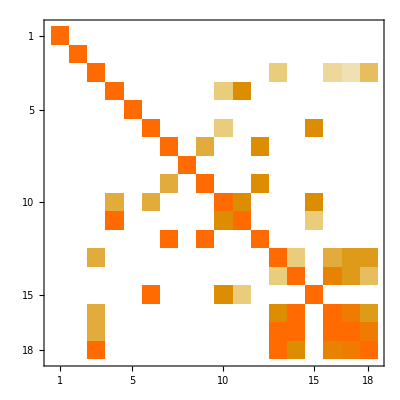

```mathematica
MatrixPlot[tablecirc]
```

```mathematica
(* x=0.88, a=1, b=4, tmax 500, z=0.89
```

```mathematica
x=0.88; a=1; b=4; tmax 500; z=0.89;
```

```mathematica
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
PositionsMatrix=Map[Flatten,Position[#,1]&/@L1];
L2=Lini; L2out=Lini;
TimeStepsN=Table[L2=Table[L3[[m]]@m,{m,1,nv}],{tmax}];
```

```mathematica
trivial0=ConstantArray[0,tmax];
trivial1=ConstantArray[1,tmax];
trivInd={};For[i=1,i≤nv,i++,If[HammingDistance[Transpose[TimeStepsN][[i]],trivial0 ]≤ 10||HammingDistance[Transpose[TimeStepsN][[i]],trivial1 ]≤ 10,trivInd=Join[trivInd,{i}],trivInd=trivInd]];
ntInd=Complement[Table[i,{i,nv}],trivInd];
ntTimeStepsN=TimeStepsN[[1;;,ntInd]];
```

```mathematica
ntCorr0=Correlation[0.5 ntTimeStepsN+0.5];
ntnv=Length[ntInd];
ntCorr1=Table[Table[If[Abs[ntCorr0[[i,j]]]>z,1,0],{j,1,ntnv}],{i,1,ntnv}];
MatrixPlot[ntCorr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ci=Table[Position[ntCorr1[[i]],1],{i,Length[ntCorr1]}];
leci=Table[Length[ci[[i]]],{i,Length[ntCorr1]}];
poleci=Table[Position[leci,i],{i,1,Max[leci]}];
cile=Table[Extract[ci,poleci[[i]]],{i,1,Max[leci]}];
circ=Flatten[Table[DeleteDuplicates[Table[Flatten[cile[[j,i]],1],{i,Length[cile[[j]]]}]],{j,2,Max[leci]}],1];
```

```mathematica
tabcirc=Table[Table[Intersection[circ[[i]],circ[[j]]],{j,Length[circ]}],{i,Length[circ]}];
```

```mathematica
MatrixForm[tabcirc]
```

({15,36} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {27,70} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {18,31} | {} | {} | {} | {} | {} | {18,31} | {} | {} | {18} | {} | {}
{} | {} | {} | {39,67} | {} | {} | {} | {} | {67} | {} | {} | {39,67} | {} | {}
{} | {} | {} | {} | {33,45} | {} | {} | {33} | {} | {33,45} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {46,69} | {} | {} | {} | {} | {} | {} | {46,69} | {69}
{} | {} | {} | {} | {} | {} | {50,66} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {33} | {} | {} | {33,76} | {} | {33,76} | {} | {} | {} | {}
{} | {} | {18,31} | {67} | {} | {} | {} | {} | {18,31,67} | {} | {} | {18,67} | {} | {}
{} | {} | {} | {} | {33,45} | {} | {} | {33,76} | {} | {33,45,76} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {38,51,61} | {} | {38} | {38,51,61}
{} | {} | {18} | {39,67} | {} | {} | {} | {} | {18,67} | {} | {} | {18,39,67} | {} | {}
{} | {} | {} | {} | {} | {46,69} | {} | {} | {} | {} | {38} | {} | {38,46,69} | {38,69}
{} | {} | {} | {} | {} | {69} | {} | {} | {} | {} | {38,51,61} | {} | {38,69} | {38,51,61,69})

```mathematica
tablecirc=Table[Table[Length[tabcirc[[i,j]]]/Length[tabcirc[[i,i]]],{i,Length[circ]}],{j,Length[circ]}];
```

```mathematica
MatrixForm[tablecirc]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 1/3 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 2/3 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1/2 | 0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1 | 0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1/2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2/3 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1/3 | 3/4
0 | 0 | 1/2 | 1 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1/3 | 0 | 1 | 1/2
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1 | 0 | 2/3 | 1)

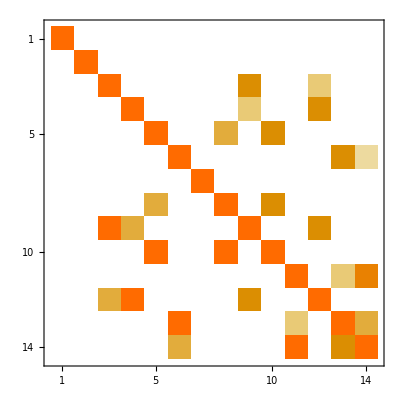

```mathematica
MatrixPlot[tablecirc]
```

```mathematica
(* x=0.88, a=1, b=4, tmax 500, z=0.9
```

```mathematica
x=0.88; a=1; b=4; tmax 500; z=0.9;
```

```mathematica
L1=Table[Table[If[connBroadmann[[i,j]]>x,1,0],{j,1,nv}],{i,1,nv}];
```

```mathematica
PositionsMatrix=Map[Flatten,Position[#,1]&/@L1];
L2=Lini; L2out=Lini;
TimeStepsN=Table[L2=Table[L3[[m]]@m,{m,1,nv}],{tmax}];
```

```mathematica
trivial0=ConstantArray[0,tmax];
trivial1=ConstantArray[1,tmax];
trivInd={};For[i=1,i≤nv,i++,If[HammingDistance[Transpose[TimeStepsN][[i]],trivial0 ]≤ 10||HammingDistance[Transpose[TimeStepsN][[i]],trivial1 ]≤ 10,trivInd=Join[trivInd,{i}],trivInd=trivInd]];
ntInd=Complement[Table[i,{i,nv}],trivInd];
ntTimeStepsN=TimeStepsN[[1;;,ntInd]];
```

```mathematica
ntCorr0=Correlation[0.5 ntTimeStepsN+0.5];
ntnv=Length[ntInd];
ntCorr1=Table[Table[If[Abs[ntCorr0[[i,j]]]>z,1,0],{j,1,ntnv}],{i,1,ntnv}];
MatrixPlot[ntCorr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ci=Table[Position[ntCorr1[[i]],1],{i,Length[ntCorr1]}];
leci=Table[Length[ci[[i]]],{i,Length[ntCorr1]}];
poleci=Table[Position[leci,i],{i,1,Max[leci]}];
cile=Table[Extract[ci,poleci[[i]]],{i,1,Max[leci]}];
circ=Flatten[Table[DeleteDuplicates[Table[Flatten[cile[[j,i]],1],{i,Length[cile[[j]]]}]],{j,2,Max[leci]}],1];
```

```mathematica
tabcirc=Table[Table[Intersection[circ[[i]],circ[[j]]],{j,Length[circ]}],{i,Length[circ]}];
```

```mathematica
MatrixForm[tabcirc]
```

({15,36} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {27,70} | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {18,31} | {} | {} | {} | {} | {} | {} | {18,31} | {} | {18}
{} | {} | {} | {38,61} | {} | {} | {} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {39,67} | {} | {} | {} | {} | {67} | {} | {39,67}
{} | {} | {} | {} | {} | {33,45} | {} | {} | {33} | {} | {33,45} | {}
{} | {} | {} | {} | {} | {} | {46,69} | {} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | {50,66} | {} | {} | {} | {}
{} | {} | {} | {} | {} | {33} | {} | {} | {33,76} | {} | {33,76} | {}
{} | {} | {18,31} | {} | {67} | {} | {} | {} | {} | {18,31,67} | {} | {18,67}
{} | {} | {} | {} | {} | {33,45} | {} | {} | {33,76} | {} | {33,45,76} | {}
{} | {} | {18} | {} | {39,67} | {} | {} | {} | {} | {18,67} | {} | {18,39,67})

```mathematica
tablecirc=Table[Table[Length[tabcirc[[i,j]]]/Length[tabcirc[[i,i]]],{i,Length[circ]}],{j,Length[circ]}];
```

```mathematica
MatrixForm[tablecirc]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 1/3
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1/3 | 0 | 2/3
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1/2 | 0 | 2/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1 | 0 | 2/3 | 0
0 | 0 | 1 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1 | 0 | 2/3
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1/2 | 0 | 1 | 0 | 0 | 0 | 0 | 2/3 | 0 | 1)

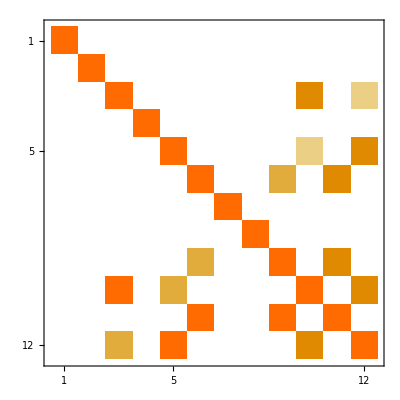

```mathematica
MatrixPlot[tablecirc]
```

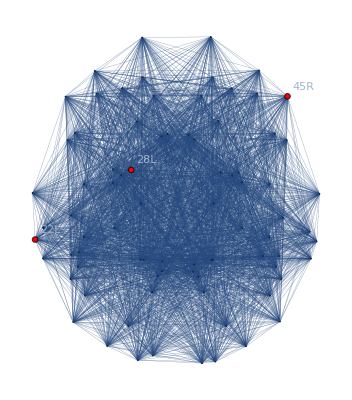

```mathematica
circ1=tabcirc[[11,11]];
GraphPlot[connBroadmann,VertexCoordinates->vertcoord,VertexLabels->Table[circ1[[i]]->vertlabel[[circ1[[i]]]],{i,Length[circ1]}],PlotStyle->Thickness[0.0005],VertexSize->Table[circ1[[i]]->5,{i,Length[circ1]}],VertexStyle->Table[circ1[[i]]->Red,{i,Length[circ1]}]]
```

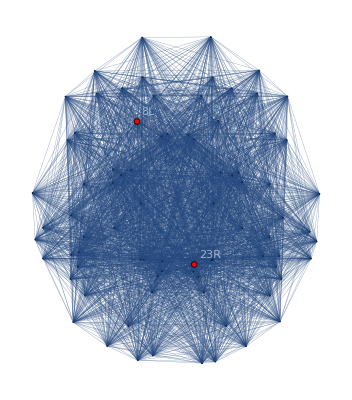

```mathematica
GraphPlot[connBroadmann,VertexCoordinates->vertcoord,VertexLabels->Table[tabcirc[[1,1]][[i]]->vertlabel[[tabcirc[[1,1]][[i]]]],{i,Length[tabcirc[[1,1]]]}],PlotStyle->Thickness[0.0005],VertexSize->Table[tabcirc[[1,1]][[i]]->5,{i,Length[tabcirc[[1,1]]]}],VertexStyle->Table[tabcirc[[1,1]][[i]]->Red,{i,Length[tabcirc[[1,1]]]}]]
```

```mathematica
circ1
```

{33,45,76}

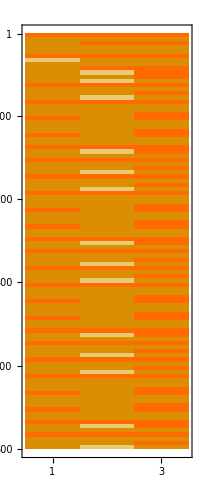

```mathematica
MatrixPlot[ntTimeStepsN[[1;;,circ1]],ColorRules->{0->Red,1->Blue}]
```

```mathematica
leOnDynamics=Table[Length[Position[Transpose[ntTimeStepsN][[i]],1]],{i,Length[Corr3]}]
```

{358,196,249,118,382,162,224,163,226,226,239,271,162,184,225,361,204,255,247,118,277,163,256,333,161,93,300,157,140,183,232,245,225,138,313,220,157,161,293,136,200,343,183,314,206,181,198,209,96,203,186,180,367,419,159,222,156,181,259,98,164,260,161,329,196,198,274,288,185,278,165,247,209,388,118,250,102,247,201,177,209,369}

```mathematica
poOnDynamics=Position[leOnDynamics,tmax]
```

{}

```mathematica
poTestDynamics=Position[leOnDynamics,30]
```

{}

```mathematica
indTest=Complement[Range[1,Length[Corr3]],Transpose[poTestDynamics][[1]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82}

```mathematica
Dimensions[ntTimeStepsN[[1;;,{15,36}]]]
```

{500,2}

```mathematica
MatrixPlot[ntTimeStepsN[[1;;,circ1]],ColorRules->{0->Red,1->Blue}]
```

-Graphics-

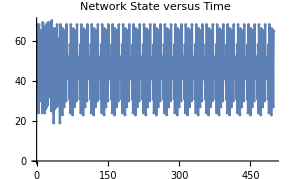

```mathematica
ListPlot[Table[HammingDistance[ntTimeStepsN[[1]],ntTimeStepsN[[nn]]],{nn,2,tmax}],Mesh->All,Joined->True,PlotLabel->"Network State versus Time",ImageSize->{290,150}]
```

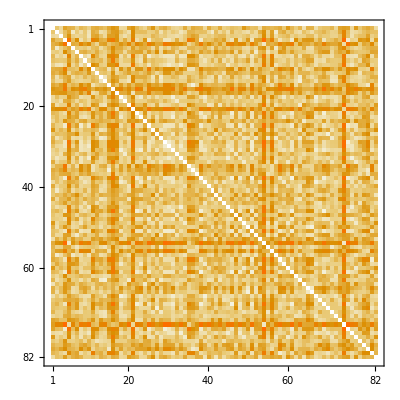

```mathematica
mc0=Table[Table[HammingDistance[Transpose[TimeStepsN][[i]],Transpose[TimeStepsN][[j]]]/500.,{i,nv}],{j,nv}];
MatrixPlot[mc0]
```

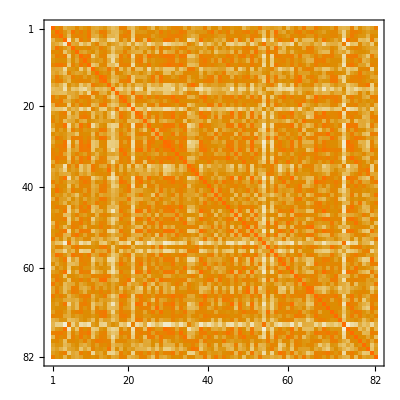

```mathematica
mc1=Table[Table[1-HammingDistance[Transpose[TimeStepsN][[i]],Transpose[TimeStepsN][[j]]]/500.,{i,nv}],{j,nv}];
MatrixPlot[mc1]
```

```mathematica
corrmc0=Correlation[mc0];
MatrixPlot[corrmc0,PlotLegends->Automatic]
```

-Graphics-

```mathematica
corrmc1=Correlation[mc1];
MatrixPlot[Abs[corrmc1],PlotLegends->Automatic]
```

-Graphics-